# A Simple Inverse Cellular Automata for Biological Evolution

User-entered Parameters

Target Lifetime lifetime to which an adaptive mutation chain should reach
Rule Bucket size number of adaptive mutation chain iterations
Max Mutation Attempts per iteration
Debug Flag

Successful Scenario of an Adaptive Mutation Chain

Lifetime reached = Target lifetime
Rule progression is plotted
Iterations per lifetime table is printed

Failed Scenarios of an Adaptive Mutation Chain

Lifetime reached > Target lifetime
Lifetime reached < Target lifetime after all unique point mutations fail
Maximum mutation attempts per iteration exceeded

Point mutation chains are run using  WL  functions RandomRuleMutation and TestLifetime

```mathematica
(*Compute lifetime of a rule given initial state*)TestLifetime[rule_Integer,init_List:{1},max_Integer:100]:=Module[{array},array=CellularAutomaton[{rule,2,2},init,{max,All}];
If[#==0,-Infinity,max-#+1]&[LengthWhile[Reverse[array],Total[#]==0&]]]

RandomRuleMutation[rule_Integer,many_Integer:1]:=Module[{ruleList,mutatedList,positions},ruleList=ruleNumberToList[rule];
positions=RandomSample[1;;Length[ruleList],many];
mutatedList=ReplacePart[ruleList,Thread[positions->Mod[ruleList[[positions]]+1,2]]];
FromDigits[mutatedList,2]  (*return mutated rule as integer*)]

CustomStyleData[key_]:=Lookup[Association["Colors"->{0->White,1->Black},"HighlightColors"->{0->White,1->Lighter[Black,0.8]},"ListPlot"->Directive[RGBColor[0.368417,0.506779,0.709798],EdgeStyle[Opacity[0.25]]]],Key[key]]
```

searchForUnfitRules simply creates a random set of rules which are constraint to a lifetime of 1 which are the ones we want to start the point mutations chains from - this is ensured when the four relevant neighbourhoods for the fixed initial condition transform to zero by the rule, hence we are fixing {0, 0, 0}→0, {0, 0, 1}→0, {0, 1, 0}→0 and {1, 0, 0}→0 (for which the least significant ternary bits are {27,26,24,18})

```mathematica
(*DEFINITIONS*)ruleNumberToList[rule_Integer]:=IntegerDigits[rule,2,32]

TestLifetime[rule_Integer,init_List:{1},max_Integer:100]:=Module[{array},array=CellularAutomaton[{rule,2,2},init,{max,All}];
If[#==0,-Infinity,max-#+1]&[LengthWhile[Reverse[array],Total[#]==0&]]]

RandomRuleMutation[rule_Integer,many_Integer:1]:=Module[{ruleList,mutatedList,positions,n},ruleList=IntegerDigits[rule,2,32];
n=Min[many,32];
positions=RandomSample[Range[32],n];
mutatedList=ReplacePart[ruleList,Thread[positions->Mod[ruleList[[positions]]+1,2]]];
FromDigits[mutatedList,2]]

searchForUnfitRules[sampleSize_:5]:=Module[{rules,r},rules={};
While[Length[rules]<sampleSize,r=RandomInteger[{0,2^32-1}];
If[TestLifetime[r,{1},20]==1,AppendTo[rules,r]]];
rules]
```

Main code, explanatory comments inline

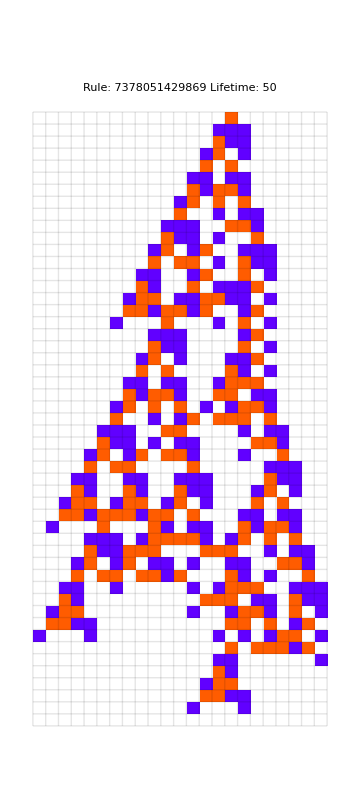
-Graphics-Lifetime | Iterations
1 | 365
2 | 16
3 | 19
6 | 45
8 | 78
10 | 4
16 | 8
39 | 1
50 | 1

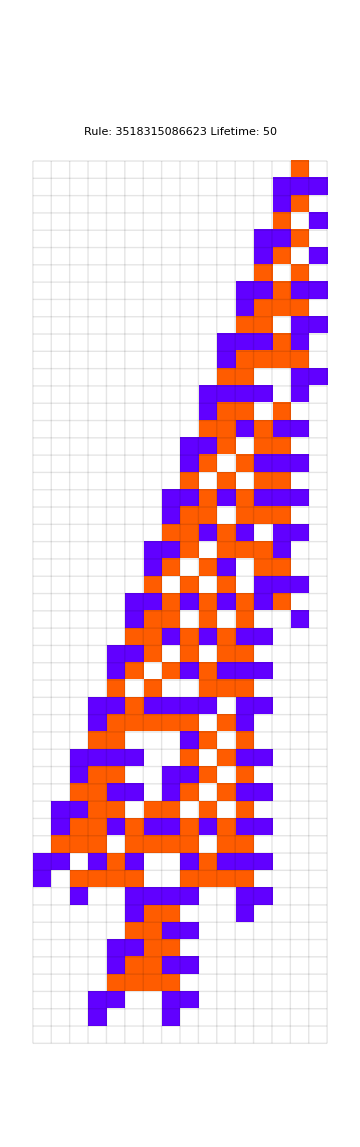
-Graphics-Lifetime | Iterations
1 | 231
2 | 71
3 | 13
4 | 17
6 | 22
7 | 3
8 | 49
9 | 17
18 | 1
22 | 28
24 | 6
41 | 1
50 | 1

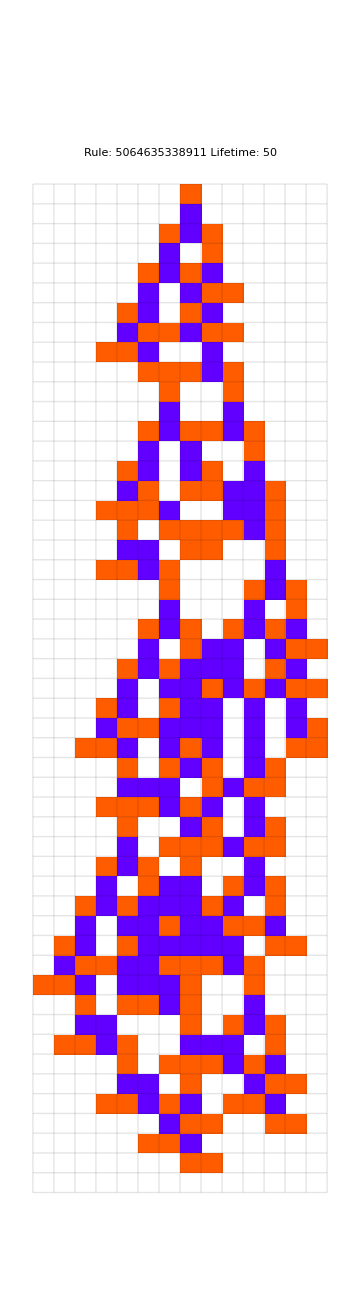
-Graphics-Lifetime | Iterations
1 | 179
4 | 18
5 | 36
6 | 32
10 | 1
11 | 3
28 | 1
41 | 1
50 | 1

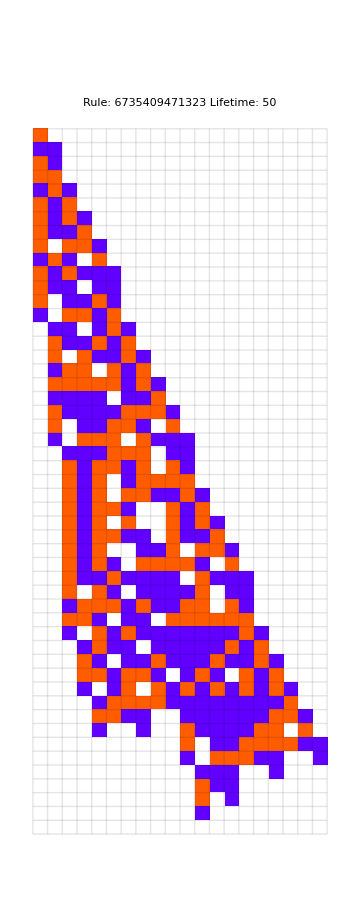
-Graphics-Lifetime | Iterations
1 | 630
2 | 17
3 | 164
4 | 56
7 | 9
10 | 38
19 | 1
50 | 1

Summary | 
Target Lifetime | 50
Number Of Mutation Chains | 100
Number Of Successful Mutation Chains | 4
Max Mutation Attempts Per Chain | 8000
Debug Flag | False

CellularAutomaton::rsize: The specified rule number 1535265876 is greater than the largest possible rule number (255).

CellularAutomaton::rsize: The specified rule number 3027873982 is greater than the largest possible rule number (255).

CellularAutomaton::rsize: The specified rule number 3705652981 is greater than the largest possible rule number (255).

General::stop: Further output of StyleBox[RowBox[{\"CellularAutomaton\", \"::\", \"rsize\"}], \"MessageName\"] will be suppressed during this calculation.

```mathematica
Module[
  {maxLifetime=200,originalRule,mutatedRule,originalLifetime,mutatedLifetime,data,k=3,lifetimeCounter=<||>,ruleSerialNumber,progressIndicator, ruleMutations,mutationsAttemptsPerRule,mutationSet, successfulChains=0},

(*Create a dialog to prompt the user for input and validate input to be positive integers*){targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize,debugFlag}=DialogInput[DynamicModule[{targetLifetime=20,maxMutationsAttemptsPerRule=500,ruleBucketSize=10,debugFlag=False},Column[{Style["Configuration (enter positive integers)",FontSize->18],
Row[{"Target Lifetime ",InputField[Dynamic[targetLifetime],Number,FieldSize->Tiny]}],Row[{"Number Of Mutation Chains ",InputField[Dynamic[ruleBucketSize],Number,FieldSize->Tiny]}],Row[{"Max Mutation Attempts Per Chain ",InputField[Dynamic[maxMutationsAttemptsPerRule],Number,FieldSize->Tiny]}],Row[{"Debug Flag ",PopupMenu[Dynamic[debugFlag],{True,False}]}],DefaultButton["OK",DialogReturn[If[And@@(IntegerQ/@{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize})&&And@@(Positive/@{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize}),{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize,debugFlag},{Null,Null,Null,Null} (*Return a list of Nulls instead of DialogReturn[{}]*)]]]}]]];

(*Check if inputs are valid*)
If[MemberQ[{targetLifetime,maxMutationsAttemptsPerRule,ruleBucketSize},Null],Return["Invalid input. Please enter positive integers for all fields."]];

(* Call searchForUnfitRules and store the result in RuleBucket which contains a list of rules with a lifetime of 1 *)    RuleBucket=searchForUnfitRules[ruleBucketSize];

(*Initialize the progress indicator*)
 ruleSerialNumber=0;
 progressIndicator=ProgressIndicator[Dynamic[ruleSerialNumber/ruleBucketSize],{0,1}];
 Print[progressIndicator];

  (* Iterate over each rule in RuleBucket *)
  Do[
    
 ruleSerialNumber++;

(*Update progress indicator*)
Pause[0.1];
 
(* Print summary of run when it is done *)
If[ruleSerialNumber==ruleBucketSize,
	Print[
		Grid[
			{
				{"Summary",""},
				{"Target Lifetime",targetLifetime},
				{"Number Of Mutation Chains",ruleBucketSize},
				{"Number Of Successful Mutation Chains",successfulChains},
				{"Max Mutation Attempts Per Chain",maxMutationsAttemptsPerRule},
				{"Debug Flag",debugFlag}
			},
			Frame->All,
			Background->{None,{LightGray,{White}}},
			ItemStyle->Directive[Bold,FontColor->Darker[Red]],
			Spacings->{2,2},
			Alignment->Center
		]
	];
  ];

    mutationsAttemptsPerRule=0;
    lifetimeCounter=<||>;
    originalRule=rule;
    originalLifetime=1;
    lifetimeCounter[originalLifetime]=1;

    (* Continuously attempt mutations *)
    While[mutationsAttemptsPerRule<maxMutationsAttemptsPerRule,
      mutationSet=<||>;
      ruleMutations=0;

      While[ruleMutations<52, (* a max of 52 point mutations per rule *)
        (* Attempt a new point mutation *)
        mutatedRule=RandomRuleMutation[{originalRule,k,1}];
        mutationsAttemptsPerRule++;

        (* Avoid repeating mutations *)
        If[!KeyExistsQ[mutationSet,mutatedRule],
          mutationSet[mutatedRule]=True;
          ruleMutations++;

          (* Test the lifetime of the mutated rule *)
          mutatedLifetime=TestLifetime[mutatedRule,maxLifetime];

          (*
          Print["Rule: ",First[mutatedRule]," ruleMutations: ",ruleMutations," totMutations: ", mutationsAttemptsPerRule," Lifetime: ",mutatedLifetime];
          *)

          If[mutationsAttemptsPerRule==maxMutationsAttemptsPerRule,
            If[debugFlag==True,
              Print["REACHED MAXIMUM MUTATIONS PER RULE! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
            ];
          ];

          (* Check if the mutated rule's lifetime is equal to or greater than the current lifetime, if so then accept mutation*)
          If[
            mutatedLifetime>=originalLifetime,
            (* Update the rule and its lifetime *)
            originalRule=First[mutatedRule];
            originalLifetime=mutatedLifetime;

            (* Update the counter for the new lifetime *)
            If[KeyExistsQ[lifetimeCounter,originalLifetime],
              lifetimeCounter[originalLifetime]++,
              lifetimeCounter[originalLifetime]=1
            ];

            (* Break to check lifetime reached and start mutating the accepted rule again if necessary *)
            Break[]
          ];
        ]
      ];

      (* If the lifetime reached exceeded the lifetime target, move to the next rule from ruleBucket *)
       If[originalLifetime>targetLifetime,
        If[debugFlag==True,
          Print["EXCEEDED TARGET! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
        ];
        Break[]
      ];

      (* If the exact lifetime target was reached, plot and move to the next rule from ruleBucket *)
      If[originalLifetime==targetLifetime,

        If[debugFlag==True,
          Print["SUCCESS! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime ];
        ];

	successfulChains++;

	data=CellularAutomaton[{originalRule,k,1},{{1},0},originalLifetime];
	
	Print[Row[
	  {
	    ArrayPlot[
	      data,
	      PlotLabel->Row[{"Rule: ",originalRule,"   Lifetime: ",originalLifetime}],
	      ImageSize->Medium,
	      ColorRules->CustomStyleData["Colors"],
	      Mesh->True,
	      MeshStyle->Opacity[.1]
	    ],
	    Spacer[50],
	    Grid[
	      {{"Lifetime","Iterations"}} ~Join~ SortBy[Normal[KeyValueMap[List,lifetimeCounter]],First],
	      Frame->All,
	      Background->{None,{LightGray,{White}}},
	      Spacings->{2,2},
	      Alignment->Center,
	      ItemStyle->Directive[Bold,FontColor->Darker[Blue]]
	    ]
	  }
	]];

        Break[]
      ];

      (* If no successful mutations are found, move to the next rule from ruleBucket *)
      If[ruleMutations>=52,
        If[debugFlag==True,
          Print["ALL 52 POINT MUTATIONS FAILED! Last Rule Number: ",originalRule," Last Lifetime: ",originalLifetime];
        ];
        Break[];
      ];
    ],
    {rule,RuleBucket}
  ]
]
```

```mathematica
(*Run this cell alone to verify*)ruleNumberToList[12345]
TestLifetime[12345,ConstantArray[0,101]~ReplacePart~{51->1},40]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,0,1}

CellularAutomaton::nocol: Since position 2 of rule specification {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,0,1},2,2} is not {}, position 1 must be an integer or a pure Boolean function.

CellularAutomaton::kspec: Since position 1 of rule specification {40,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1} or {k, wts}, where k is a machine integer > 1 and wts is a nonempty array of non-negative machine integers.

-∞

```mathematica
SCHEMATA CODE
```

```mathematica
(*MAIN CODE*)k=2;
r=2;
steps=35;
width=101;
targetLifetime=26;
maxRestarts=150;
mutationsPerRestart=2000;

Module[{init,currentRule,currentLifetime,currentDist,found,candidate,candidateLifetime,candidateDist,bestRule,bestLifetime,bestDist,unfitPool,verifiedLifetime,restartCount,ruleNumber,lookupTable,neighborhoods,lookupVisual,caData,phenotypeVisual},init=ConstantArray[0,width];
init[[Ceiling[width/2]]]=1;
found=False;
bestDist=Infinity;
restartCount=0;
Print["=== SEARCH LOG ==="];
Print["Target lifetime: ",targetLifetime];
Print["Every restart begins from lifetime 1 (via searchForUnfitRules)"];
Print[""];
Do[If[found,Break[]];
restartCount++;
unfitPool=searchForUnfitRules[1];
currentRule=unfitPool[[1]];
verifiedLifetime=TestLifetime[currentRule,init,steps];
Print["Restart ",restartCount," | Starting rule: ",currentRule," | Starting lifetime: ",If[verifiedLifetime==-Infinity,1,verifiedLifetime]];
currentLifetime=1;
currentDist=Abs[1-targetLifetime];
Do[If[found,Break[]];
candidate=RandomRuleMutation[currentRule,RandomInteger[{1,3}]];
candidateLifetime=TestLifetime[candidate,init,steps];
candidateDist=Abs[candidateLifetime-targetLifetime];
If[candidateDist<=currentDist,currentRule=candidate;
currentLifetime=candidateLifetime;
currentDist=candidateDist;
If[currentDist==0,found=True;
bestRule=currentRule;bestLifetime=currentLifetime;bestDist=0;
Print["  >>> FOUND at restart ",restartCount," | Rule: ",currentRule," | Lifetime: ",currentLifetime]]],{mutationsPerRestart}];
If[!found,Print["  End of restart ",restartCount," | Climbed to lifetime ",currentLifetime," (distance ",currentDist,")"]];
If[!found&&currentDist<bestDist,bestRule=currentRule;bestLifetime=currentLifetime;bestDist=currentDist],{maxRestarts}];
Print[""];
Print["=== SEARCH COMPLETE ==="];
If[!found,Print["Did not converge. Closest lifetime: ",bestLifetime," (distance ",bestDist,")."],Print["Found rule ",bestRule," with lifetime ",bestLifetime];
Print[""];
ruleNumber=bestRule;
lookupTable=IntegerDigits[ruleNumber,2,32];
neighborhoods=Reverse[Tuples[{0,1},2 r+1]];
lookupVisual=Grid[Table[{ArrayPlot[{neighborhoods[[i]]},ColorRules->{0->White,1->Black},Mesh->True,MeshStyle->Directive[Gray,Thin],Frame->False,ImageSize->100],Style["→",16],ArrayPlot[{{lookupTable[[i]]}},ColorRules->{0->White,1->Black},Mesh->True,MeshStyle->Directive[Gray,Thin],Frame->False,ImageSize->40]},{i,32}],Spacings->{2,1},Alignment->Center];
caData=CellularAutomaton[{ruleNumber,k,r},init,steps];
phenotypeVisual=ArrayPlot[caData,ColorRules->{0->White,1->Black},Mesh->True,MeshStyle->Directive[Gray,Thin],Frame->True,ImageSize->400,PlotLabel->Row[{"Rule: ",ruleNumber,"  |  Lifetime: ",bestLifetime}]];
Row[{Column[{Style["Genotype (Lookup Table)",16,Bold],lookupVisual}],Spacer[50],Column[{Style["Phenotype (CA Evolution)",16,Bold],phenotypeVisual}]}]]]
```

=== SEARCH LOG ===

Target lifetime: 26

Every restart begins from lifetime 1 (via searchForUnfitRules)

Restart 1 | Starting rule: 1298741706 | Starting lifetime: 1

End of restart 1 | Climbed to lifetime 1 (distance 25)

Restart 2 | Starting rule: 112465854 | Starting lifetime: 1

End of restart 2 | Climbed to lifetime 1 (distance 25)

Restart 3 | Starting rule: 524875914 | Starting lifetime: 1

End of restart 3 | Climbed to lifetime 1 (distance 25)

Restart 4 | Starting rule: 1915783428 | Starting lifetime: 1

End of restart 4 | Climbed to lifetime 16 (distance 10)

Restart 5 | Starting rule: 715630154 | Starting lifetime: 1

End of restart 5 | Climbed to lifetime 20 (distance 6)

Restart 6 | Starting rule: 2136389502 | Starting lifetime: 1

End of restart 6 | Climbed to lifetime 1 (distance 25)

Restart 7 | Starting rule: 1642552066 | Starting lifetime: 1

End of restart 7 | Climbed to lifetime 1 (distance 25)

Restart 8 | Starting rule: 347534098 | Starting lifetime: 1

End of restart 8 | Climbed to lifetime 18 (distance 8)

Restart 9 | Starting rule: 589437142 | Starting lifetime: 1

End of restart 9 | Climbed to lifetime 1 (distance 25)

Restart 10 | Starting rule: 586846622 | Starting lifetime: 1

End of restart 10 | Climbed to lifetime 1 (distance 25)

Restart 11 | Starting rule: 960526148 | Starting lifetime: 1

End of restart 11 | Climbed to lifetime 1 (distance 25)

Restart 12 | Starting rule: 1808393980 | Starting lifetime: 1

End of restart 12 | Climbed to lifetime 1 (distance 25)

Restart 13 | Starting rule: 1525888390 | Starting lifetime: 1

End of restart 13 | Climbed to lifetime 1 (distance 25)

Restart 14 | Starting rule: 64320780 | Starting lifetime: 1

End of restart 14 | Climbed to lifetime 1 (distance 25)

Restart 15 | Starting rule: 334558196 | Starting lifetime: 1

End of restart 15 | Climbed to lifetime 1 (distance 25)

Restart 16 | Starting rule: 2022586256 | Starting lifetime: 1

End of restart 16 | Climbed to lifetime 18 (distance 8)

Restart 17 | Starting rule: 1649305058 | Starting lifetime: 1

End of restart 17 | Climbed to lifetime 1 (distance 25)

Restart 18 | Starting rule: 464422178 | Starting lifetime: 1

End of restart 18 | Climbed to lifetime 1 (distance 25)

Restart 19 | Starting rule: 1756027926 | Starting lifetime: 1

End of restart 19 | Climbed to lifetime 8 (distance 18)

Restart 20 | Starting rule: 409872834 | Starting lifetime: 1

End of restart 20 | Climbed to lifetime 12 (distance 14)

Restart 21 | Starting rule: 391060324 | Starting lifetime: 1

End of restart 21 | Climbed to lifetime 1 (distance 25)

Restart 22 | Starting rule: 1568133602 | Starting lifetime: 1

End of restart 22 | Climbed to lifetime 1 (distance 25)

Restart 23 | Starting rule: 1423201116 | Starting lifetime: 1

End of restart 23 | Climbed to lifetime 29 (distance 3)

Restart 24 | Starting rule: 1899874564 | Starting lifetime: 1

End of restart 24 | Climbed to lifetime 1 (distance 25)

Restart 25 | Starting rule: 492859466 | Starting lifetime: 1

End of restart 25 | Climbed to lifetime 1 (distance 25)

Restart 26 | Starting rule: 1060537268 | Starting lifetime: 1

End of restart 26 | Climbed to lifetime 21 (distance 5)

Restart 27 | Starting rule: 411099480 | Starting lifetime: 1

End of restart 27 | Climbed to lifetime 1 (distance 25)

Restart 28 | Starting rule: 1168492824 | Starting lifetime: 1

End of restart 28 | Climbed to lifetime 1 (distance 25)

Restart 29 | Starting rule: 992424946 | Starting lifetime: 1

End of restart 29 | Climbed to lifetime 1 (distance 25)

Restart 30 | Starting rule: 998694832 | Starting lifetime: 1

End of restart 30 | Climbed to lifetime 22 (distance 4)

Restart 31 | Starting rule: 1537349866 | Starting lifetime: 1

End of restart 31 | Climbed to lifetime 1 (distance 25)

Restart 32 | Starting rule: 953201552 | Starting lifetime: 1

End of restart 32 | Climbed to lifetime 16 (distance 10)

Restart 33 | Starting rule: 85795142 | Starting lifetime: 1

End of restart 33 | Climbed to lifetime 1 (distance 25)

Restart 34 | Starting rule: 2081142152 | Starting lifetime: 1

>>> FOUND at restart 34 | Rule: 3099731380 | Lifetime: 26

=== SEARCH COMPLETE ===

Found rule 3099731380 with lifetime 26

Genotype (Lookup Table)
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Phenotype (CA Evolution)
-Graphics-

Restart 42 | Starting rule: 1392408410 | Starting lifetime: 1

End of restart 41 | Climbed to lifetime 1 (distance 14)

Restart 41 | Starting rule: 1612810526 | Starting lifetime: 1

End of restart 40 | Climbed to lifetime 1 (distance 14)

Restart 40 | Starting rule: 1440708672 | Starting lifetime: 1

End of restart 39 | Climbed to lifetime 1 (distance 14)

Restart 39 | Starting rule: 1507189282 | Starting lifetime: 1

End of restart 38 | Climbed to lifetime 1 (distance 14)

Restart 38 | Starting rule: 1374742098 | Starting lifetime: 1

End of restart 37 | Climbed to lifetime 1 (distance 14)

Restart 37 | Starting rule: 1785371840 | Starting lifetime: 1

End of restart 36 | Climbed to lifetime 1 (distance 14)

Restart 36 | Starting rule: 1044819834 | Starting lifetime: 1

End of restart 35 | Climbed to lifetime 1 (distance 14)

Restart 35 | Starting rule: 1027714880 | Starting lifetime: 1

End of restart 34 | Climbed to lifetime 1 (distance 14)

Restart 34 | Starting rule: 379142124 | Starting lifetime: 1

End of restart 33 | Climbed to lifetime 8 (distance 7)

Restart 33 | Starting rule: 110249242 | Starting lifetime: 1

End of restart 32 | Climbed to lifetime 1 (distance 14)

Restart 32 | Starting rule: 1561364818 | Starting lifetime: 1

End of restart 31 | Climbed to lifetime 1 (distance 14)

Restart 31 | Starting rule: 1266502534 | Starting lifetime: 1

End of restart 30 | Climbed to lifetime 1 (distance 14)

Restart 30 | Starting rule: 1202046544 | Starting lifetime: 1

End of restart 29 | Climbed to lifetime 9 (distance 6)

Restart 29 | Starting rule: 780470498 | Starting lifetime: 1

End of restart 28 | Climbed to lifetime 7 (distance 8)

Restart 28 | Starting rule: 771775776 | Starting lifetime: 1

End of restart 27 | Climbed to lifetime 1 (distance 14)

Restart 27 | Starting rule: 516621816 | Starting lifetime: 1

End of restart 26 | Climbed to lifetime 2 (distance 13)

Restart 26 | Starting rule: 1857949246 | Starting lifetime: 1

End of restart 25 | Climbed to lifetime 1 (distance 14)

Restart 25 | Starting rule: 1640208194 | Starting lifetime: 1

End of restart 24 | Climbed to lifetime 1 (distance 14)

Restart 24 | Starting rule: 1147219862 | Starting lifetime: 1

End of restart 23 | Climbed to lifetime 1 (distance 14)

Restart 23 | Starting rule: 534535902 | Starting lifetime: 1

End of restart 22 | Climbed to lifetime 1 (distance 14)

Restart 22 | Starting rule: 1396184454 | Starting lifetime: 1

End of restart 21 | Climbed to lifetime 8 (distance 7)

Restart 21 | Starting rule: 145303840 | Starting lifetime: 1

End of restart 20 | Climbed to lifetime 1 (distance 14)

Restart 20 | Starting rule: 1758896448 | Starting lifetime: 1

End of restart 19 | Climbed to lifetime 1 (distance 14)

Restart 19 | Starting rule: 1092351622 | Starting lifetime: 1

End of restart 18 | Climbed to lifetime 1 (distance 14)

Restart 18 | Starting rule: 1736825970 | Starting lifetime: 1

End of restart 17 | Climbed to lifetime 1 (distance 14)

Restart 17 | Starting rule: 1111839526 | Starting lifetime: 1

End of restart 16 | Climbed to lifetime 1 (distance 14)

Restart 16 | Starting rule: 1231444862 | Starting lifetime: 1

End of restart 15 | Climbed to lifetime 1 (distance 14)

Restart 15 | Starting rule: 947115374 | Starting lifetime: 1

End of restart 14 | Climbed to lifetime 4 (distance 11)

Restart 14 | Starting rule: 1570246404 | Starting lifetime: 1

End of restart 13 | Climbed to lifetime 7 (distance 8)

Restart 13 | Starting rule: 459336632 | Starting lifetime: 1

End of restart 12 | Climbed to lifetime 1 (distance 14)

Restart 12 | Starting rule: 2093529102 | Starting lifetime: 1

End of restart 11 | Climbed to lifetime 1 (distance 14)

Restart 11 | Starting rule: 1930395060 | Starting lifetime: 1

End of restart 10 | Climbed to lifetime 1 (distance 14)

Restart 10 | Starting rule: 712894370 | Starting lifetime: 1

End of restart 9 | Climbed to lifetime 1 (distance 14)

Restart 9 | Starting rule: 208530700 | Starting lifetime: 1

End of restart 8 | Climbed to lifetime 1 (distance 14)

Restart 8 | Starting rule: 2088726342 | Starting lifetime: 1

End of restart 7 | Climbed to lifetime 1 (distance 14)

Restart 7 | Starting rule: 1201956318 | Starting lifetime: 1

End of restart 6 | Climbed to lifetime 1 (distance 14)

Restart 6 | Starting rule: 1165751450 | Starting lifetime: 1

End of restart 5 | Climbed to lifetime 2 (distance 13)

Restart 5 | Starting rule: 1276296492 | Starting lifetime: 1

End of restart 4 | Climbed to lifetime 1 (distance 14)

Restart 4 | Starting rule: 1253781958 | Starting lifetime: 1

End of restart 3 | Climbed to lifetime 1 (distance 14)

Restart 3 | Starting rule: 1403144436 | Starting lifetime: 1

End of restart 2 | Climbed to lifetime 1 (distance 14)

Restart 2 | Starting rule: 93133658 | Starting lifetime: 1

End of restart 1 | Climbed to lifetime 1 (distance 14)

Restart 1 | Starting rule: 1551009824 | Starting lifetime: 1

Every restart begins from lifetime 1 (via searchForUnfitRules)

Target lifetime: 15

=== SEARCH LOG ===

```mathematica
□
```